```mathematica
v[t]/.DSolve[{v'[t]==-k v[t],v[0]==v0},v[t],t][[1]]
```

ⅇ^(-k t) v0

```mathematica
Integrate[%4,{t,0,t}]
```

(v0-ⅇ^(-k t) v0)/k

```mathematica
x[t_,k_,v0_]:=(v0-ⅇ^(-k t) v0)/k;
```

```mathematica
Limit[%11,t->Infinity]
```

ConditionalExpression[v0/k, v0∈ℝ&&k>0]

```mathematica
x[t,1,5]
```

5-5 ⅇ^-t

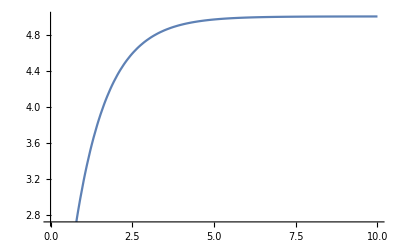

```mathematica
Plot[x[t,1,5],{t,0,10}]
```

```mathematica
Manipulate[
DiscretePlot[(Binomial[kTotal,k]Binomial[total-kTotal,n-k])/Binomial[total,n],{k,0,total}],
{total,0,100,1},
{kTotal,0,100,1},
{n,0,100,1}
]
```

```mathematica
(n+1)(kTotal+1)/(total+2)/.{n->11,kTotal->5,total->15}//N
```

4.23529

```mathematica
Manipulate[
DiscretePlot[Binomial[n,k] p^k(1-p)^(n-k),{k,0,20}],
{p,0,1},
{n,0,100,1}
]
```

```mathematica
Manipulate[
DiscretePlot[Binomial[n,k] p^k(1-p)^(n-k),{n,0,100}],
{p,0,1},
{k,0,100,1}
]
```

```mathematica
v0=12
```

```mathematica
u=10
```

10

```mathematica
g=10
```

10

```mathematica
a=2
```

2

```mathematica
Clear["`*"]
```

```mathematica
Clear[a,g,u,v0,vx,vy]
```

```mathematica
a=10Degree;g=10;u=0.1;v0=2;
```

```mathematica
result=NDSolve[{
vx[0]==v0,
vy[0]==0,
vx'[t]==-(u g Cos[a] vx[t])/(√(vx[t]^2+vy[t]^2)),
vy'[t]==-(u g Cos[a] vy[t])/(√(vx[t]^2+vy[t]^2))+g Sin[a]
},{vx[t],vy[t]},{t,0,10}]
```

{{vx[t]→InterpolatingFunction[…][t],vy[t]→InterpolatingFunction[…][t]}}

```mathematica
r=vx[t]/.result[[1]];vx[t_]:=Evaluate@r;
r=vy[t]/.result[[1]];vy[t_]:=Evaluate@r;
```

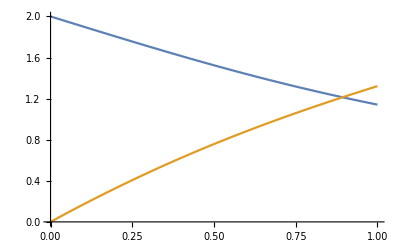

```mathematica
Plot[{vx[t],vy[t]},{t,0,1},PlotRange->All]
```

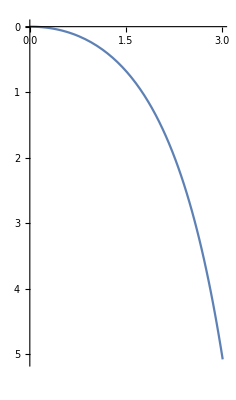

```mathematica
ParametricPlot[{
Integrate[vx[x],{x,0,t}],
Integrate[vy[x],{x,0,t}]
},{t,0,3},ScalingFunctions->{Automatic,"Reverse"}]
```

```mathematica
NDSolve[{
vx[0]==v0,
vy[0]==0,
vx'[0]==0,
vy'[0]==g Sin[a],
vx'[t]==-(u g Cos[a] vx[t])/(√(vx[t]^2+vy[t]^2)),
vy'[t]==-(u g Cos[a] vy[t])/(√(vx[t]^2+vy[t]^2))+g Sin[a]
},{vx[t],vy[t]},{t,0,10}]
```

NDSolve::ndnco: The number of constraints (4) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (2).

NDSolve[{vx[0]==2,vy[0]==0,vx'[0]==0,vy'[0]==10 Sin[10 °],vx'[t]==-(0.984808 vx[t])/(√(vx[t]^2+vy[t]^2)),vy'[t]==10 Sin[10 °]-(0.984808 vy[t])/(√(vx[t]^2+vy[t]^2))},{vx[t],vy[t]},{t,0,10}]

```mathematica
NDSolve[{
vx[0]==v0,
vy'[0]==g Sin[a],
vx'[t]==-(u g Cos[a] vx[t])/(√(vx[t]^2+vy[t]^2)),
vy'[t]==-(u g Cos[a] vy[t])/(√(vx[t]^2+vy[t]^2))+g Sin[a]
},{vx[t],vy[t]},{t,0,10}]
```

{{vx[t]→InterpolatingFunction[…][t],vy[t]→InterpolatingFunction[…][t]}}

```mathematica
NDSolve[{
vx[0]==v0,
vy[0]==0,
vx'[t]==-(u g Cos[a] vx[t])/(√(vx[t]^2+vy[t]^2)),
vy'[t]==-(u g Cos[a] vy[t])/(√(vx[t]^2+vy[t]^2))+g Sin[a]
},{vx[t],vy[t]},{t,0,10}]
```

{{vx[t]→InterpolatingFunction[…][t],vy[t]→InterpolatingFunction[…][t]}}

```mathematica
Clear["`*"]
```

```mathematica
DSolve[{
vx[0]==v0,
vy[0]==0,
vx'[0]==0,
vy'[0]==g Sin[a],
vx'[t]==-(u g Cos[a] vx[t])/(√(vx[t]^2+vy[t]^2)),
vy'[t]==-(u g Cos[a] vy[t])/(√(vx[t]^2+vy[t]^2))+g Sin[a]
},{vx[t],vy[t]},t,Assumptions->{t>0,vx[t]>0,vy[t]>0}]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

General::stop: Further output of Solve::inex will be suppressed during this calculation.

DSolve[{vx[0]==2,vy[0]==0,vx'[0]==0,vy'[0]==10 Sin[10 °],vx'[t]==-(0.984808 vx[t])/(√(vx[t]^2+vy[t]^2)),vy'[t]==10 Sin[10 °]-(0.984808 vy[t])/(√(vx[t]^2+vy[t]^2))},{vx[t],vy[t]},t,Assumptions→{t>0,vx[t]>0,vy[t]>0}]